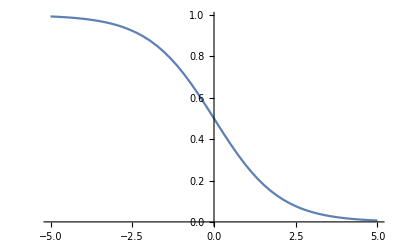

```mathematica
F[x_]:=1/(1+Exp[x]);
Plot[F[x],{x,-5,5}]
```

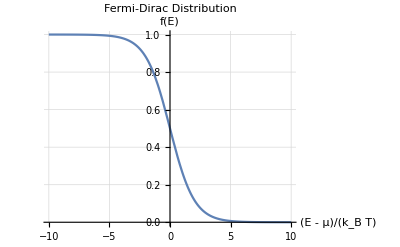

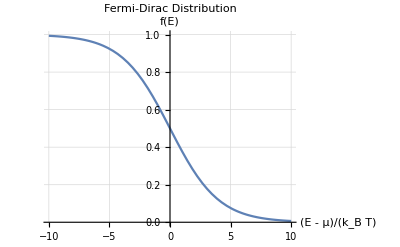

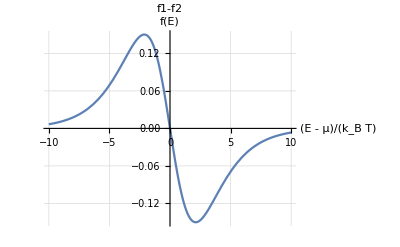

```mathematica
Plot[1/(1+Exp[x]),{x,-10,10},AxesLabel->{"(E - μ)/(k_B T)","f(E)"},PlotLabel->"Fermi-Dirac Distribution",GridLines->Automatic]
Plot[1/(1+Exp[x/2]),{x,-10,10},PlotRange->{0,1},AxesLabel->{"(E - μ)/(k_B T)","f(E)"},PlotLabel->"Fermi-Dirac Distribution",GridLines->Automatic]
Plot[(1/(1+Exp[x]))-(1/(1+Exp[x/2])),{x,-10,10},AxesLabel->{"(E - μ)/(k_B T)","f(E)"},PlotLabel->"f1-f2",GridLines->Automatic]
```

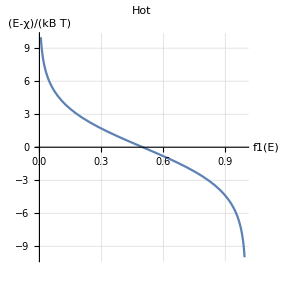

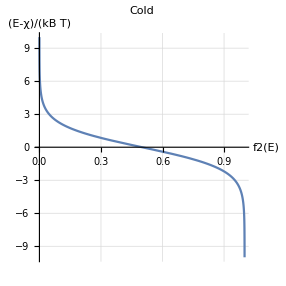

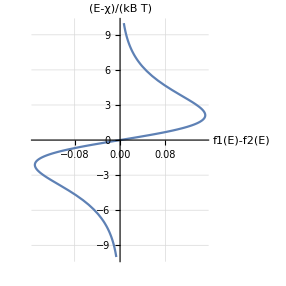

```mathematica
ParametricPlot[{1/(1+Exp[x/2]),x},{x,-10,10},AspectRatio->1,AxesLabel->{"f1(E)","(E-χ)/(kB T)"},PlotLabel->"Hot",GridLines->Automatic]
ParametricPlot[{1/(1+Exp[x]),x},{x,-10,10},AspectRatio->1,AxesLabel->{"f2(E)","(E-χ)/(kB T)"},PlotLabel->"Cold",GridLines->Automatic]
ParametricPlot[{(1/(1+Exp[x/2]))-(1/(1+Exp[x])),x},{x,-10,10},AspectRatio->1,AxesLabel->{"f1(E)-f2(E)","(E-χ)/(kB T)"},GridLines->Automatic]
```

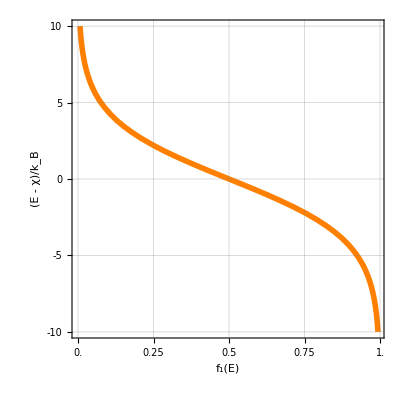

```mathematica
ParametricPlot[{1/(1+Exp[x/2]),x},{x,-10,10},AspectRatio->1,Axes->True,GridLines->{{0.00,.25,0.50,0.75,1.00},{-10,-5,0,5,10}},PlotTheme->"Scientific",FrameLabel->{{HoldForm["(E - χ)/k_B"],None},{HoldForm["f_1(E)"],HoldForm["Hot(T = T_1)"]}},AxesStyle->Black,LabelStyle->{14,GrayLevel[0],Bold},FrameStyle->Directive[Black,16],FrameTicks->{{{-10,-5,0,5,10},None},{{0.00,.25,0.50,0.75,1.00},None}},PlotStyle->{Orange,Thickness[0.01]}]
```

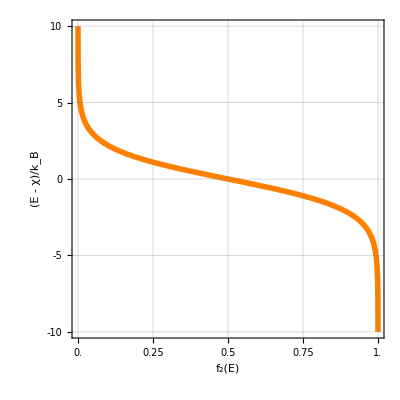

```mathematica
ParametricPlot[{1/(1+Exp[x]),x},{x,-10,10},AspectRatio->1,Axes->True,GridLines->{{0.00,.25,0.50,0.75,1.00},{-10,-5,0,5,10}},PlotTheme->"Scientific",FrameLabel->{{HoldForm["(E - χ)/k_B"],None},{HoldForm["f_2(E)"],HoldForm["Cold(T = T_2)"]}},AxesStyle->Black,LabelStyle->{14,GrayLevel[0],Bold},FrameStyle->Directive[Black,16],FrameTicks->{{{-10,-5,0,5,10},None},{{0.00,.25,0.50,0.75,1.00},None}},PlotStyle->{Orange,Thickness[0.01]}]
```

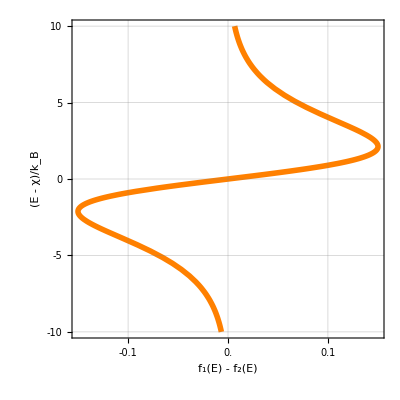

```mathematica
ParametricPlot[{(1/(1+Exp[x/2]))-(1/(1+Exp[x])),x},{x,-10,10},AspectRatio->1,Axes->True,GridLines->{{-0.1,0.0,0.1},{-10,-5,0,5,10}},PlotTheme->"Scientific",FrameLabel->{{HoldForm["(E - χ)/k_B"],None},{HoldForm["f_1(E) - f_2(E)"],HoldForm["Hot-Cold"]}},AxesStyle->Black,LabelStyle->{14,GrayLevel[0],Bold},FrameStyle->Directive[Black,16],FrameTicks->{{{-10,-5,0,5,10},None},{{-0.1,0.0,0.1},None}},PlotStyle->{Orange,Thickness[0.01]}]
```